# Thesis Notebook

## 2D Orbit with the suns density profile and mass function, along with dissipative forces

## Setting functions up and choosing variables

```mathematica
(*R values in Schwarzschild coordinates*)
RStar = 8;(*Radius of the Star*)
M = 1;
```

## Exterior Schwarzschild Isotropic coordinates definitions r(r̄), r̄(r), A(r̄), α(r̄)

### r(r̄) and r̄(r) functions

```mathematica
(*Block function says use this value of M then forget it*)

rofrbarOutside[rbar_] = Block[{M = 1}, rbar (1 + M/(2 rbar))^2]; 

rbarofrOutside[r_] = Block[{M = 1}, 1/2 (-M + r + Sqrt[r^2 - 2 M r])];
```

### A(r̄), α(r̄)

```mathematica
A[rbar_] = Block[{M=1}, (1 + M/(2 rbar))^2];
α[rbar_] = Block[{M=1}, (1 - M/(2 rbar))/(1 + M/(2 rbar))];
```

Getting the value of the radius of the star in isotropic coordinates

```mathematica
rbarStar = rbarofrOutside[RStar] //  N;
```

## TOV Isotropic coords definitions

### Mass and Density functions from 2405.08113

#### Fixing the rho0 by letting the total mass integral equal to 1

```mathematica
rho[r_] := rho0(1 - r/R)^6;
massIntegral =  4 Pi Integrate[rho[r] r^2, {r, 0, R}]; (*Set equal to 1*)
```

```mathematica
rhoCentre[R_] := 63/(Pi R^3) (*From the above*)
rho0 = rhoCentre[RStar] //N;
```

```mathematica
MassFunc[r_] := Piecewise[{{252(r^9/(9 RStar^9)-(3 r^8)/(4 RStar^8)+(15 r^7)/(7 RStar^7)-(10 r^6)/(3 RStar^6)+(3 r^5)/RStar^5-(3 r^4)/(2 RStar^4)+r^3/(3 RStar^3)) , r < RStar},
{M, r >= RStar}
}];
(*In 2405.08113 this function is divided by the solar mass, here I use M=1*)
```

### New density function

```mathematica
rho[r_] := Piecewise[{
{rho0(1 - r/RStar)^6, r < RStar},
{0, r >= RStar}
}
];
```

### Getting new equations for the new interior metric:

```mathematica
(*TOV differential equation*)
dPdr[r_, Pressure_] := -Simplify[MassFunc[r]/r^2(rho[r] + Pressure)(1 + (4 Pi (Pressure) r^3)/MassFunc[r])(1 - (2 MassFunc[r])/r)^-1];
```

```mathematica
(*Phi differential equation for metric*)
dPhidrMetric[r_, Pressure_] := Simplify[MassFunc[r]/r^2(1 + (4 Pi (Pressure) r^3)/MassFunc[r])(1 - (2 MassFunc[r])/r)^-1];
```

#### Numerically Integrate these two partially coupled differential equations

```mathematica
rmin = 10^-16 (*For these integrations*);
```

```mathematica
eq1 = P'[r] == dPdr[r, P[r]];
eq2 = Phi'[r] == dPhidrMetric[r, P[r]];
ICs = {P[RStar] == 0, Phi[RStar] == 1/2 Log[1-2 M/RStar]} ;(*Phi[RStar] from the Schwarzschild metric*)
```

```mathematica
sol1 = NDSolve[
{eq1,
eq2,
ICs},
{P, Phi},
{r, rmin, RStar}
][[1]]; (*Very small rmin to avoid singularity sarp mentioned*)
```

```mathematica
(*Maybe extrapolated points after the region of interest I solved is causing problems?*)
```

```mathematica
Pressure[r_] = Piecewise[
{
{P[r] /. sol1, r <=RStar},
{0, r > RStar}
}
];

PhiMetric[r_] = Piecewise[
{
{Phi[r] /. sol1, r <=RStar},
{-0.14384103622589042, r>RStar}
}
];
```

#### Solving for the new r̄(r) and r(r̄) inside, obtaining r(r̄) via the interpolation trick Sarp explained

```mathematica
(*Defining the ODE*)
drbardr[rbar_, r_] := rbar/r(1 - (2MassFunc[r])/r)^(-1/2)
```

Numerically Integrating the above equation.

```mathematica
eq = rbarofr'[r] == drbardr[rbarofr[r], r];
BC = {rbarofr[RStar] == rbarStar};
```

```mathematica
sol2 = NDSolve[
{eq,
BC},
{rbarofr},
{r, rmin, RStar}
][[1]];
```

```mathematica
rbarofrInside[r_] = rbarofr[r] /. sol2;
```

Now using the interpolation trick to obtain r(r̄):

```mathematica
(*Generating the numerical data points:*)
(*Table[ expression, {variable, start, end, step}*)
data = Table[
{rbarofrInside[r], r}, (*Here Mathematica stores rbar[r] and r as a 2 element list - first entry is the independent variable and the one after is the dependent variable*)
{r, 0, RStar, (RStar - 0)/500} (*500 points*)
];
```

```mathematica
(*Evaluates ok at zero as sarp mentioned but integral doesn't like it one bit*)
```

```mathematica
(*Inverse Interpolation*)
rofrbarInside = Interpolation[data];(*Builds a function from the data passing through all points unlike Fit which approximately matches the data to a function I give it with parameters,  FindFit finds the parameters for me given I guess a suitable function*)
```

```mathematica
rofrbarInside[rbarStar]
```

8.

```mathematica
rofrbarInside[rbar0]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

16.6857

```mathematica
drdrbar[rbar_, r_] := r/rbar(1 - (2MassFunc[r])/r)^(1/2)
```

```mathematica
eq = rofrbar'[r] == drbardr[rofrbar[r], r];
BC = {rofrbar[rbarStar] == RStar};
```

```mathematica
sol2 = NDSolve[
{eq,
BC},
{rofrbar},
{r, rmin, rbarStar}
][[1]];
```

```mathematica
rofrbarInside2[rbar_] := rofrbar[rbar] /. sol2;
```

```mathematica
rofrbarInside2[rbar0]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

-4364.14

### Putting this together to find the new interior metric functions

```mathematica
αInside[rbar_] := Exp[PhiMetric[rofrbarInside[rbar]]]
```

```mathematica
αInside[rbarStar];
α[rbarStar];
```

```mathematica
AInside[rbar_] := rofrbarInside[rbar]/rbar;
```

```mathematica
A[rbarStar];
AInside[rbar0]
rbar0
```

1.06613

15.6507

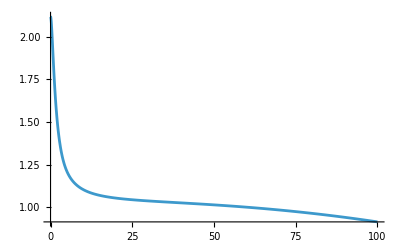

```mathematica
Plot[{AInside[rbar]}, {rbar, 0, 100}, PlotRange->All, Exclusions->None]
```

### Sorting out the speed of sound as a function of r: a(r)

```mathematica
(*Getting the derivative of the density*)
rhodummy[r_] := rho0(1 - r/RStar)^6

drhodr[r_] := rhodummy'[r]
```

```mathematica
asos[r_] := (dPdr[r, Pressure[r]]/drhodr[r])^(1/2);
```

```mathematica
cutoffRStar = RStar.9999
```

7.9992

```mathematica
asos[cutoffRStar]
```

0.00166688

```mathematica
(*asos[RStar];*) (*Infinite*)
asos[10^-12]; (*zero does not work but small r does!*)
asos[cutoffRStar]
```

0.00166688

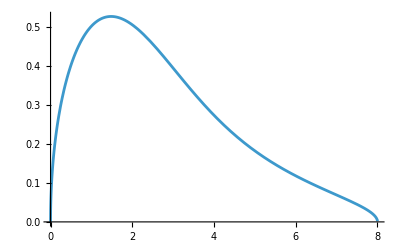

```mathematica
Plot[asos[r], {r, 0, cutoffRStar}]
```

#### Gets very messy from here downwards doing it the Taylor expansion way

```mathematica
(*Limit[asos[r], r-> RStar] //  N (*goes to infinity when I sub in*);

Limit[
FullSimplify[
Series[asos[r], {r, RStar, 5}],
r>0
],
r-> RStar
]; *)
```

The above complex infinity is the issue discussed with Sarp, must Taylor expand.

```mathematica
Pdoubleprime[r_] := D[dPdr[x, Pressure[x]], x] /. x->r  (*Must use D as ' only differentiates wrt. the first argument*)
```

```mathematica
asosprimenearRStar[r_] := 1/(2 √asos[r])(Pdoubleprime[r]/drhodr[r] - dPdr[r, Pressure[r]]/(drhodr[r])^2 drhodr'[r])
asosprimenearRStar[7.974] // N;
```

```mathematica
epsilon = 0.026; (*from RStar - 7.974 which is oscillating only in the 1e-4 range for alphaprime which is very small*)
```

```mathematica
asosprimenearRStar[7.974]*epsilon (*could either use this?*)
```

-0.000476814

Attempting to double differentiate and see where the function hits zero to find the max and minimum value of a’ in order to find the value of r to make a(r) a minimum

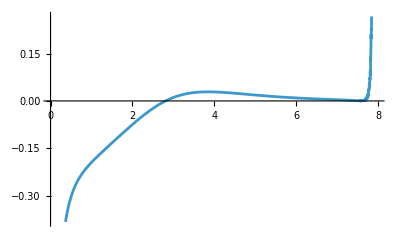

```mathematica
Plot[asosprimenearRStar'[r], {r, 0, 7.984}]
```

```mathematica
func[r_] := Pdoubleprime[r]/drhodr[r] - dPdr[r, Pressure[r]]/(drhodr[r])^2 drhodr'[r]
func[.999*RStar];
```

```mathematica
Pdoubleprime[RStar*.999]/drhodr[RStar*.999];
```

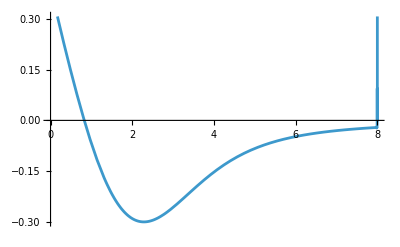

```mathematica
Plot[Pdoubleprime[r]/drhodr[r], {r, 0, RStar}]
```

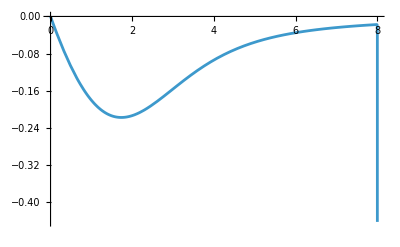

```mathematica
Plot[dPdr[r, Pressure[r]]/(drhodr[r])^2 drhodr'[r], {r, 0, RStar}]
```

#### Speed of sound in isotropic coordinates

```mathematica
sosStarBoundary = rbarofrInside[cutoffRStar]
rbarStar;
Abs[sosStarBoundary-rbarStar] (*Very close*)
```

6.9633

0.000804146

```mathematica
asosPiecewise[rbar_] := Piecewise[
{
{10^-6, rbar <10^-8},
{asos[rofrbarInside[rbar]], rbar <= sosStarBoundary},
{asos[rofrbarInside[sosStarBoundary]], sosStarBoundary< rbar < rbarStar},
{10^-6, rbar > rbarStar}
}
];
```

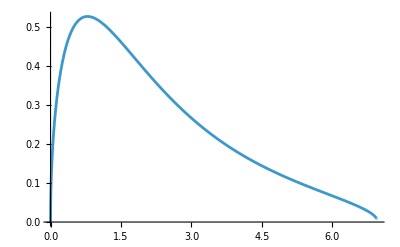

```mathematica
Plot[asosPiecewise[rbar], {rbar, 0, rbarStar}, PlotRange-> All]
```

#### Density and Pressure in isotropic coordinates

```mathematica
rho0 = rhoCentre[RStar] //N;
```

```mathematica
rho[rbar_] :=Piecewise[
{
{rho0(1 - rofrbarInside[rbar]/RStar)^6, rbar <= rbarStar},
{0, rbar > rbarStar}
}
];

IsotropicCoordsPressure[rbar_] := Piecewise[
{
{Pressure[rofrbarInside[rbar]], rbar <= rbarStar},
{0, rbar > rbarStar}
}
]; (*Defined above*)
```

## Setting up system for new density profile:

Constants that are going to be used

```mathematica
m = 10^-6; (*mass of PBH?*)
λGR[rbar_] := 1.49*asosPiecewise[rbar] (*Made redundant now after cancelling the a's in the accretion*)
q = 2;
η= 10; (*Speed up parameter 72.5 is nice*)
```

### Mach number interpolation

#### Interpolating

```mathematica
x1 = 1; (*Deleted prev graph*)
x2 = 1;
y1 = 3.03;
y2 = 6.67;

anaylticline[Μach_] := y1 + (y2 - y1) (x - x1)/(x2 - x1);
```

```mathematica
IVariableInterpolated[Μach_] := Piecewise[{
{1/2 Log[(1+ Μach)/(1 - Μach)] - Μach, Μach < 0.9999},
{anaylticline[Μach], 0.9999 < Μach  < 1.0001},
{1/2 Log[1 - 1/Μach^2]  + 10, Μach > 1.0001}
}];
```

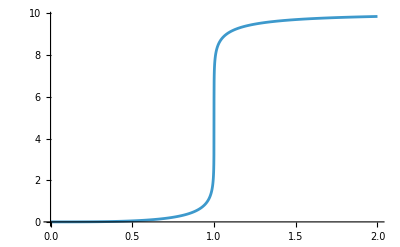

```mathematica
Plot[IVariableInterpolated[Mach], {Mach, 0, 2}, PlotRange->All, Exclusions->None]
```

### Outside Star

#### Velocities

```mathematica
Ut[rbar_, ur_, uphi_] := (√(1 + (ur/A[rbar])^2 + (uphi/(rbar A[rbar]))^2))/α[rbar];
```

#### Rates of change of velocities

```mathematica
drBardt[rbar_, ur_, uphi_] := 1/(A[rbar]^2 Ut[rbar, ur, uphi])ur;

dphidtOutside[rbar_,ur_, uphi_] := 1/(rbar^2*A[rbar]^2*Ut[rbar, ur,uphi])uphi;

durdt2DOutside[rbar_, ur_, uphi_] := -α[rbar] Ut[rbar, ur, uphi] Derivative[1][α][rbar] + ur^2/Ut[rbar, ur, uphi]((Derivative[1][A][rbar])/A[rbar]^3) + uphi^2/Ut[rbar, ur, uphi](1/(rbar^3 *A[rbar]^2) + (Derivative[1][A][rbar])/(rbar^2*A[rbar]^3));
```

### Inside Star

#### Mach Number

```mathematica
asosPiecewise[rbar_] := Piecewise[
{
{10^-4, rbar <10^-8},
{asos[rofrbarInside[rbar]], rbar <= sosStarBoundary},
{asos[rofrbarInside[sosStarBoundary]], sosStarBoundary< rbar < rbarStar},
{10^-4, rbar > rbarStar}
}
];
```

```mathematica
Mach[rbar_, ur_, uphi_] := Piecewise[{
{umagphi[rbar, ur, uphi]/(asosPiecewise[rbar]  α[rbar] Ut[rbar, ur, uphi]), rbar > rbarStar},
{umagphi[rbar, ur, uphi]/(asosPiecewise[rbar] αInside[rbar] UtInside[rbar, ur, uphi]), rbar <= rbarStar}
}
];
```

#### Velocities

```mathematica
UtInside[rbar_, ur_, uphi_] := (√(1 + (ur/AInside[rbar])^2 + (uphi/(rbar AInside[rbar]))^2))/αInside[rbar];
umagphi[rbar_, ur_, uphi_] := Piecewise
[
{
{(√(ur^2+(uphi/rbar)^2))/AInside[rbar], rbar <rbarStar},
{(√(ur^2+(uphi/rbar)^2))/A[rbar], rbar >= rbarStar}
}
];(*paper eqn ut and umagphi*)
```

#### Mass accretion

```mathematica
(* for Γ = 2 accretion rate*) (*This is my dmdt equation*)

mdot[m_, rbar_, ur_, uphi_] := 1.49* (4Pi rho0 m^2)/(asosPiecewise[rbar]^2 + (umagphi[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2); (*Ask Sarp about this rho0*) (*Paper mentions main accretion near the centre so maybe this is correct to use?*)


(*dpdtaccretionr[m_, rbar_, ur_, uphi_] := -Simplify[((4 Pi αInside[rbar] λGR[rbar](rho[rbar] + IsotropicCoordsPressure[rbar])m^2)/asosPiecewise[rbar]^3)(asosPiecewise[rbar]^2/(asosPiecewise[rbar]^2+(umagphi[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2))^(q/2)]ur;


dpdtaccretionphi[m_, rbar_, ur_, uphi_] := -Simplify[((4 Pi αInside[rbar] λGR[rbar](rho[rbar] + IsotropicCoordsPressure[rbar])m^2)/asosPiecewise[rbar]^3)(asosPiecewise[rbar]^2/(asosPiecewise[rbar]^2+(umagphi[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2))^(q/2)]uphi;*)
```

#### Mass accretion in this regime has no a dependence

```mathematica
dpdtaccretionr[m_, rbar_, ur_, uphi_] := -((4 Pi αInside[rbar] (1.49)(rho[rbar] + IsotropicCoordsPressure[rbar])m^2))(1/(asosPiecewise[rbar]^2+(umagphi[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2))^(q/2)ur;

dpdtaccretionphi[m_, rbar_, ur_, uphi_] := -((4 Pi αInside[rbar] (1.49)(rho[rbar] + IsotropicCoordsPressure[rbar])m^2))(1/(asosPiecewise[rbar]^2+(umagphi[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2))^(q/2)uphi;
```

#### Hydrodynamic drag forces

```mathematica
dpdtdragphi[m_, rbar_, ur_, uphi_] := 1/umagphi[rbar, ur, uphi]^3(-4π αInside[rbar]*(rho[rbar] + IsotropicCoordsPressure[rbar])*m^2*(1 + 2 umagphi[rbar, ur, uphi]^2)^2 *IVariableInterpolated[Mach[rbar, ur, uphi]] *uphi);


dpdtdragr[m_, rbar_, ur_, uphi_] := (-4π αInside[rbar](rho[rbar] + IsotropicCoordsPressure[rbar])m^2(1 + 2 umagphi[rbar, ur, uphi]^2)^2 IVariableInterpolated[Mach[rbar, ur, uphi]] *ur)/umagphi[rbar, ur, uphi]^3;
```

#### Rates of change of “velocities”

```mathematica
drBardtInside[rbar_, ur_, uphi_] := 1/(AInside[rbar]^2 UtInside[rbar, ur, uphi])ur;

dphidtInside[rbar_, ur_, uphi_] := 1/(rbar^2 AInside[rbar]^2 UtInside[rbar, ur, uphi])uphi;

duphidtInside[m_, rbar_, ur_, uphi_] := η/m(dpdtdragphi[m, rbar, ur, uphi] + dpdtaccretionphi[m, rbar, ur, uphi]);

durdt2DInside[m_, rbar_, ur_, uphi_] := -αInside[rbar] UtInside[rbar, ur, uphi] Derivative[1][αInside][rbar] + ur^2/UtInside[rbar, ur, uphi]((Derivative[1][AInside][rbar])/AInside[rbar]^3) + uphi^2/UtInside[rbar, ur, uphi](1/(rbar^3 AInside[rbar]^2) + (Derivative[1][AInside][rbar])/(rbar^2 AInside[rbar]^3)) +  η/m(dpdtdragr[m, rbar, ur, uphi]+ dpdtaccretionr[m, rbar, ur, uphi]);
```

### Defining orbital parameters: Energy and Angular momentum per unit mass

```mathematica
EnergyPerUnitMass[ptilde_, eccen_] := √(((ptilde -2)^2 - 4 *eccen^2)/(ptilde*(ptilde - 3 - eccen^2)));
LPerUnitMass[ptilde_, M_, eccen_] := (ptilde*M)/(√(ptilde - 3 - eccen^2));
ptildefunc[p_, Mass_] := p/Mass;
rapoapsis[eccen_, ptilde_, Mass_] := ((ptilde)*Mass)/(1 - eccen); (*In Schwarzschild areal r coordinates*)
rperiapsis[eccen_, ptilde_] := ptilde/(1+eccen);
```

### Defining the constants to define the motion

#### Eccentricity and semi-latus rectum

```mathematica
eccentricity = 0.4;
semilatrecP = 10;
ptilde = ptildefunc[semilatrecP, M];
```

#### Energy and Angular momentum per unit mass

```mathematica
Energy = EnergyPerUnitMass[ptilde, eccentricity];
AngularMomentumUphi0 = LPerUnitMass[ptilde, M, eccentricity];
```

#### Initial drop radius (apoapsis), closest point it goes to (perihelion), defining Isotropic star radius

```mathematica
r0 = rapoapsis[eccentricity, ptilde, M];
rbar0 = rbarofrOutside[r0];
```

#### Must satisfy this inequality to pass through star

```mathematica
ptilde < RStar(1+eccentricity)
ptilde > 6 + 2eccentricity
```

True

True

```mathematica
durdt2DInside[m,rbar0,0,AngularMomentumUphi0]
```

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Power::infy: Infinite expression 1/0 encountered.

0.00266583

```mathematica
Mach[rbar0,0,AngularMomentumUphi0]
umagphi[rbar0,0,AngularMomentumUphi0]
```

9746.79 Piecewise

Piecewise

## Solving the ODEs

```mathematica
(*asosPiecewise[rbar_] := Piecewise[
{
{0.5, rbar>0}
}
]*)
(*umagphi=0.5*)
```

```mathematica
t0=0;
tEnd=2000;

solIn=NDSolve[
{
rbar'[t]==
Piecewise[
{
{drBardt[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{drBardtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
ur'[t]==
Piecewise[
{
{durdt2DOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{durdt2DInside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
uphi'[t]==
Piecewise[
{
{0,rbar[t]>=rbarStar},
{duphidtInside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
phi'[t]==
Piecewise[
{
{dphidtOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{dphidtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
mass'[t]==
Piecewise[
{
{0,rbar[t]>=rbarStar},
{mdot[mass[t], rbar[t], ur[t], uphi[t]],rbar[t]<rbarStar}
}
],
rbar[0]== rbar0,
ur[0]==0,
phi[0]==0,
uphi[0]==AngularMomentumUphi0,
mass[0] == m,

WhenEvent[rbar[t] <= 10^-3 , "StopIntegration"]
},
{rbar,ur,phi,uphi, mass},
{t,t0,tEnd},
MaxSteps->20000
][[1]];
```

Power::infy: Infinite expression 1/0 encountered.

InterpolatingFunction::dmval: Input value {15.6507} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

NDSolve::ndinid: Initial condition Sign[Max[0.9999-9746.79 Piecewise,-1.0001+9746.79 Piecewise]] is not in the range specified by the discrete variable NDSolve`s$9430.

```mathematica
rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
phiNumIn = phi /. solIn;
uphiNumIn = uphi /. solIn;
massNumIn = mass /. solIn;
```

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
tFinish = rbarNumIn["Domain"][[1,2]]
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}]
```

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification … is longer than depth of object.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification … is longer than depth of object.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification … is longer than depth of object.

FindRoot::bbound: Search region bound … for variable number 1 is not a number or Infinity.

ReplaceAll::reps: {FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

Part::partd: Part specification … is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FindRoot::bbound: Search region bound … for variable number 1 is not a number or Infinity.

t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}]

```mathematica
outFigRadial=Show[Plot[{rbarNumIn[t],urNumIn[t],urNumIn'[t]},{t,t0,tFinish},PlotLegends->LineLegend[Automatic,{"r̄(t)","(ū)_r(t)","(ū)_r'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification … is longer than depth of object.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification … is longer than depth of object.

Plot::plln: Limiting value … in {t,0,(rbar/.{rbar'[t]==Piecewise[{{«2»},{«2»}},0],ur'[t]==Piecewise[{{«2»},{«2»}},0],uphi'[t]==Piecewise[{{«2»},{«2»}},0],phi'[t]==Piecewise[{{«2»},{«2»}},0],mass'[t]==Piecewise[{{«2»},{«2»}},0],rbar[0]==15.6507,ur[0]==0,phi[0]==0,uphi[0]==3.8236,mass[0]==1/1000000,WhenEvent[rbar[t]≤1/10^3,StopIntegration]})[Domain]⟦1,2⟧} is not a machine-sized real number.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

Part::partd: Part specification … is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FindRoot::bbound: Search region bound … for variable number 1 is not a number or Infinity.

General::stop: Further output of FindRoot::bbound will be suppressed during this calculation.

Plot::plln: Limiting value t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}] in {t,t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}],(rbar/.{rbar'[t]==Piecewise[{«2»},0],ur'[t]==Piecewise[{«2»},0],uphi'[t]==Piecewise[{«2»},0],phi'[t]==Piecewise[{«2»},0],mass'[t]==Piecewise[{«2»},0],rbar[0]==15.6507,ur[0]==0,phi[0]==0,uphi[0]==3.8236,mass[0]==1/1000000,WhenEvent[rbar[«1»]≤Power[«2»],StopIntegration]})[Domain]⟦1,2⟧+(t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}])} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{rbarNumIn[t],urNumIn[t],urNumIn'[t]},{t,t0,tFinish},PlotLegends→LineLegend[Automatic,{r̄(t),(ū)_r(t),(ū)_r'(t)}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle→Directive[Gray,Opacity[0.1]],Filling→Bottom]].

$Aborted

```mathematica
outFigAngular=Plot[{uphiNumIn[t],uphiNumIn'[t]},{t,t0,tFinish},PlotLegends->LineLegend[Automatic,{"phi(t)","uphi(t)","uphi'(t)"}]]
```

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification … is longer than depth of object.

Plot::plln: Limiting value … in {t,0,(rbar/.{rbar'[t]==Piecewise[{{«2»},{«2»}},0],ur'[t]==Piecewise[{{«2»},{«2»}},0],uphi'[t]==Piecewise[{{«2»},{«2»}},0],phi'[t]==Piecewise[{{«2»},{«2»}},0],mass'[t]==Piecewise[{{«2»},{«2»}},0],rbar[0]==15.6507,ur[0]==0,phi[0]==0,uphi[0]==3.8236,mass[0]==1/1000000,WhenEvent[rbar[t]≤1/10^3,StopIntegration]})[Domain]⟦1,2⟧} is not a machine-sized real number.

Plot[{uphiNumIn[t],uphiNumIn'[t]},{t,t0,tFinish},PlotLegends→LineLegend[Automatic,{phi(t),uphi(t),uphi'(t)}]]

```mathematica
outFigMass=Show[Plot[{massNumIn[t],massNumIn''[t]},{t,t0, tFinish},PlotLegends->LineLegend[Automatic,{"m(t)","m'(t)"}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle->Directive[Gray,Opacity[0.1]],Filling->Bottom]]
```

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification … is longer than depth of object.

Plot::plln: Limiting value … in {t,0,(rbar/.{rbar'[t]==Piecewise[{{«2»},{«2»}},0],ur'[t]==Piecewise[{{«2»},{«2»}},0],uphi'[t]==Piecewise[{{«2»},{«2»}},0],phi'[t]==Piecewise[{{«2»},{«2»}},0],mass'[t]==Piecewise[{{«2»},{«2»}},0],rbar[0]==15.6507,ur[0]==0,phi[0]==0,uphi[0]==3.8236,mass[0]==1/1000000,WhenEvent[rbar[t]≤1/10^3,StopIntegration]})[Domain]⟦1,2⟧} is not a machine-sized real number.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification … is longer than depth of object.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

Part::partd: Part specification … is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

FindRoot::bbound: Search region bound … for variable number 1 is not a number or Infinity.

General::stop: Further output of FindRoot::bbound will be suppressed during this calculation.

Plot::plln: Limiting value t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}] in {t,t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}],(rbar/.{rbar'[t]==Piecewise[{«2»},0],ur'[t]==Piecewise[{«2»},0],uphi'[t]==Piecewise[{«2»},0],phi'[t]==Piecewise[{«2»},0],mass'[t]==Piecewise[{«2»},0],rbar[0]==15.6507,ur[0]==0,phi[0]==0,uphi[0]==3.8236,mass[0]==1/1000000,WhenEvent[rbar[«1»]≤Power[«2»],StopIntegration]})[Domain]⟦1,2⟧+(t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}])} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{massNumIn[t],massNumIn''[t]},{t,t0,tFinish},PlotLegends→LineLegend[Automatic,{m(t),m'(t)}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle→Directive[Gray,Opacity[0.1]],Filling→Bottom]].

Plot::plln: Limiting value … in {t,0,(rbar/.{rbar'[t]==Piecewise[{{«2»},{«2»}},0],ur'[t]==Piecewise[{{«2»},{«2»}},0],uphi'[t]==Piecewise[{{«2»},{«2»}},0],phi'[t]==Piecewise[{{«2»},{«2»}},0],mass'[t]==Piecewise[{{«2»},{«2»}},0],rbar[0]==15.6507,ur[0]==0,phi[0]==0,uphi[0]==3.8236,mass[0]==1/1000000,WhenEvent[rbar[t]≤1/10^3,StopIntegration]})[Domain]⟦1,2⟧} is not a machine-sized real number.

General::stop: Further output of Plot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[Plot[{massNumIn[t],massNumIn''[t]},{t,t0,tFinish},PlotLegends→LineLegend[Automatic,{m(t),m'(t)}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle→Directive[Gray,Opacity[0.1]],Filling→Bottom]].

Show[Plot[{massNumIn[t],massNumIn''[t]},{t,t0,tFinish},PlotLegends→LineLegend[Automatic,{m(t),m'(t)}]],Plot[rbarStar,{t,tSurface,tSurface+tFinish},PlotStyle→Directive[Gray,Opacity[0.1]],Filling→Bottom]]

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

Part::partd: Part specification … is longer than depth of object.

ParametricPlot::plln: Limiting value 0.999 (rbar/.{rbar'[t]==Piecewise[{{«2»},{«2»}},0],ur'[t]==Piecewise[{{«2»},{«2»}},0],uphi'[t]==Piecewise[{{«2»},{«2»}},0],phi'[t]==Piecewise[{{«2»},{«2»}},0],mass'[t]==Piecewise[{{«2»},{«2»}},0],rbar[0]==15.6507,ur[0]==0,phi[0]==0,uphi[0]==3.8236,mass[0]==1/1000000,WhenEvent[rbar[t]≤1/10^3,StopIntegration]})[Domain]⟦1,2⟧ in {t,0,0.999 (rbar/.{rbar'[t]==Piecewise[{«2»},0],ur'[t]==Piecewise[{«2»},0],uphi'[t]==Piecewise[{«2»},0],phi'[t]==Piecewise[{«2»},0],mass'[t]==Piecewise[{«2»},0],rbar[0]==15.6507,ur[0]==0,phi[0]==0,uphi[0]==3.8236,mass[0]==1/1000000,WhenEvent[rbar[«1»]≤Power[«2»],StopIntegration]})[Domain]⟦1,2⟧} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[,ParametricPlot[{x[t],y[t]},{t,t0,0.999 tFinish},AspectRatio→Automatic,AxesLabel→{x,y},PlotRange→All,PlotStyle→{Thick,Blue}],AspectRatio→Automatic,PlotRange→All,Axes→True].

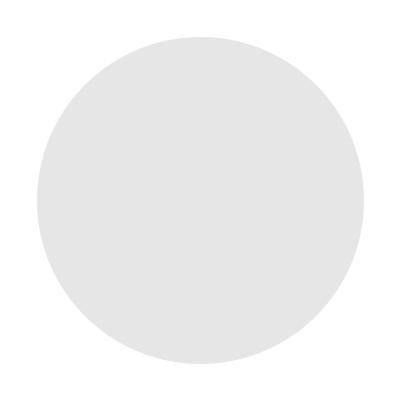
Show[-Graphics-,ParametricPlot[{x[t],y[t]},{t,t0,0.999 tFinish},AspectRatio→Automatic,AxesLabel→{x,y},PlotRange→All,PlotStyle→{Thick,Blue}],AspectRatio→Automatic,PlotRange→All,Axes→True]

```mathematica
x[t_]:=rbarNumIn[t] Cos[phiNumIn[t]];
y[t_]:=rbarNumIn[t] Sin[phiNumIn[t]];
orbit2D=ParametricPlot[{x[t],y[t]},{t,t0,0.999 tFinish},AspectRatio->Automatic,AxesLabel->{"x","y"},PlotRange->All,PlotStyle->{Thick,Blue}];
(*Automatic scale makes the aces the same scale*)
centralBody=Graphics[{GrayLevel[0.9],Disk[{0,0},rbarStar]}];
Show[centralBody, orbit2D,AspectRatio->Automatic,PlotRange->All, Axes -> True]
```